```mathematica
(*Да,программа короткая-используется пара-тройка формул.Во-первых,последовательными итерациями решается уравнение для нахождения запаздывающего момента времени $t'$:$$c(t-t')=r(t')$$.
Здесь $r(t')=\sqrt{(x-s(t'))^2+y^2}$-расстояние от заряда до точки наблюдения $(x,\,y)$ в момент $t'$,а $s(t)$-текущая координата заряда.Во-вторых,сама формула для потенциала
$$\varphi(x,\,y,\,t)=\frac{q}{r(t')-\vec{v}(t')\cdot\vec{r}(t')/c}$$
или
$$\varphi(x,\,y,\,t)=\frac{q}{c(t-t')-v(t')(x-s(t'))/c}$$,где $v(t)=ds(t)/dt$-скорость заряда.*)
vk=0.84; (* конечная скорость *)
```

```mathematica
(*a= 0.3; *)(* ускорение *)
```

```mathematica
epsilon = 10^(-10); (* погрешность *)
```

```mathematica
(*t0=vk/a; *)(*время разгона*)
```

```mathematica
(*s[t_]:=If[t<0,0, If[t<t0, a*t^2/2, vk *t-a * t0^2/2]];*)(*координата от времени*)
(*Стоп,а правильно ли Дробышев записал формулу для координаты от времени? Пусть t=7.5 сек.Тогда за время равноускоренного движения заряд пройдёт расстояние a*t0^2/2=0,3*2,8*2,8/2=1,176 световых (неважно-пикосекунд,наносекунд или микросекунд).За оставшееся время (t-t0) заряд пройдёт vk*(t-t0)+a*t0^2/2. 
0.84*(7.5-2.8)+1.1176=5.0656 ед.
Итого формулу нужно переписать так*)
s[t_]:=vk*t;(*координата от времени*)(*Удивительно,что столько умных мужиков до сих пор не заметили ошибку уровня 7 класса школы:))*)
```

```mathematica
v[t_]:=vk; (*скорость от времени*)
```

```mathematica
phi[x_,y_,t_]:=Module[{t1,t2}, t1=t; t2=t-2* epsilon;(*расчёт итерациями запаздывающего момента t2 *)
While[Abs[t1-t2]>epsilon, t1=t2; t2=t-Sqrt[(x-s[t1])^2+y^2]];(*при расчетах $r$ можно заменить на $c(t-t')$*)
1./(t-t2-v[t2]* (x-s[t2])) (*скалярный потенциал по Линару-Вихерту*)
];
```

```mathematica
ss=
Table[Show[ContourPlot[phi[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,0.08,0.36,0.02}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]], {t,0,30,0.25}];
Export["D://lienar-wiechert_v_const.gif",ss]
```

D://lienar-wiechert_v_const.gif

```mathematica
"D://lienar-wiechert_v_const.gif"
```

D://lienar-wiechert_v_const.gif

```mathematica
"D://lienar-wiechert_.gif"
```

D://lienar-wiechert_.gif

```mathematica
t=7.5;
```

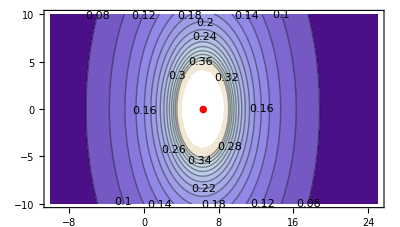

```mathematica
Show[ContourPlot[phi[x,y,t],{x,-10,25},{y,-10,10},
Contours->Table[k,{k,0.08,0.36,0.02}], PlotPoints->40, AspectRatio->Automatic, ContourLabels->True],
Graphics[{Red, Disk[{s[t],0},0.4]}]]
```

```mathematica
ss2=
Table[Show[Plot3D[phi[x,y,t],{x,-10,25},{y,-10,10}]], {t,0,30,0.25}];
Export["D://lienar-wiechert_t_zap.gif",ss2]
```

D://lienar-wiechert_t_zap.gif

```mathematica
"D://lienar-wiechert-plot3d.gif"
```

D://lienar-wiechert-plot3d.gif

```mathematica
ss3=
Table[Plot3D[phi[x,y,t],{x,-10,25},{y,-10,10}], {t,0,50,2}];
Export["D://lienar-wiechert_correct-plot3d3.gif",ss3]
```

D://lienar-wiechert_correct-plot3d3.gif

```mathematica
"D://lienar-wiechert_correct-plot3d3.gif"
```

D://lienar-wiechert_correct-plot3d3.gif

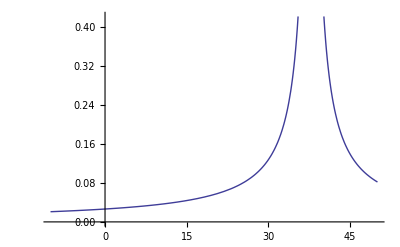

```mathematica
t=45;Plot[phi[x,0,t],{x,-10,50}]
```

```mathematica
Value[phi[x,0,t],{x,-10,50}]
```

Value[1./(√((-37.8+x)^2)-0.84 (-0.84 (45-√((-37.8+x)^2))+x)),{x,-10,50}]